# 2.2 2D linear System

## a) EigValues of A

```mathematica
A = {{sigma+1,3},{-2,sigma-1}}//Simplify
```

{{1+sigma,3},{-2,-1+sigma}}

```mathematica
Eigenvalues[A]//Simplify
```

{-ⅈ √5+sigma,ⅈ √5+sigma}

## b) Solve the dynamicals system

```mathematica
ClearAll["Global'*"]
eq1=x'[t]==(sigma+1) x[t]+3 y[t];
eq2=y'[t]==-2 x[t]+(sigma-1) y[t];

initialConditions={x[0]==u,y[0]==v};

solution=DSolve[{eq1,eq2,initialConditions},{x,y},t];

(*Output the solution*)
solution // Simplify
```

{{x→Function[{t},1/5 ⅇ^(sigma t) (5 Cos[√5 t]+4 √5 Sin[√5 t])],y→Function[{t},-1/5 ⅇ^(sigma t) (-5 Cos[√5 t]+3 √5 Sin[√5 t])]}}

## c) Plot the found trajectories with simga = {-0.1, 0, 0.1}

```mathematica
Clear[u,v,sigma]
```

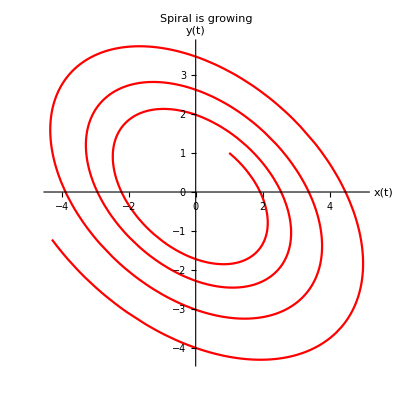

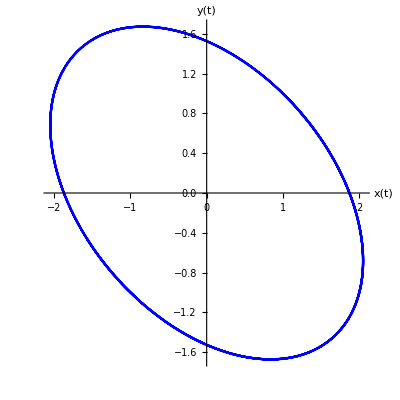

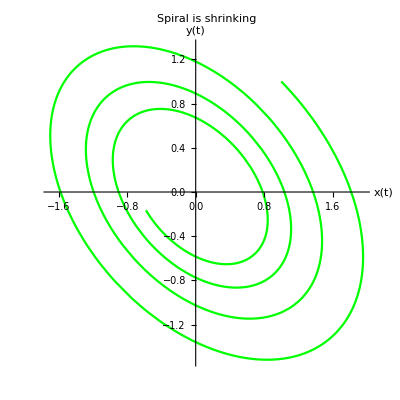

```mathematica
x[t_] := 1/5 ⅇ^(sigma t) (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t]);
y[t_]:=-1/5 ⅇ^(sigma t) (-5 v Cos[√5 t]+2 √5 u Sin[√5 t]+√5 v Sin[√5 t]);
(* Plot the trajectory *)
(*ParametricPlot[{x[t],y[t]}/. {sigma->0.1}, {t,0,10,PlotRange->All,AspectRatio->1,AxesLabel->{"x(t)","y(t)"}]*)
(*Define the time range for the plot*)tRange={t,tMin,tMax};

(*Plot the trajectory*)
p1 = ParametricPlot[{x[t],y[t]}/. {sigma->0.1, u-> 1,v->1}, {t,0,10},PlotRange->All,AspectRatio->1,AxesLabel->{"x(t)","y(t)"}, PlotStyle->Red, PlotLabel->"Spiral is growing"]
p2 = ParametricPlot[{x[t],y[t]}/. {sigma->0, u-> 1,v->1}, {t,0,10},PlotRange->All,AspectRatio->1,AxesLabel->{"x(t)","y(t)"}, PlotStyle->Blue]
p3 = ParametricPlot[{x[t],y[t]}/. {sigma->-0.1, u-> 1,v->1}, {t,0,10},PlotRange->All,AspectRatio->1,AxesLabel->{"x(t)","y(t)"}, PlotStyle->Green, PlotLabel->"Spiral is shrinking"]
Show[p1,p2,p3];
```

## d) for sigma = 0 compute the period of the ellipse

```mathematica
(* For which period T is the *)
```

```mathematica
xs[t_] = x[t]/.sigma->0
ys[t_] = y[t]/.sigma->0
```

1/5 (5 u Cos[√5 t]+√5 u Sin[√5 t]+3 √5 v Sin[√5 t])

1/5 (5 v Cos[√5 t]-2 √5 u Sin[√5 t]-√5 v Sin[√5 t])

```mathematica
Solve[xs[T]==xs[0],T]
Solve[ys[T]==ys[0],T]
```

{{T→ConditionalExpression[(2 π C[1])/(√5), C[1]∈ℤ]},{T→ConditionalExpression[(ArcTan[(4 u^2-6 u v-9 v^2)/(3 (2 u^2+2 u v+3 v^2)),(2 (√5 u^2+3 √5 u v))/(3 (2 u^2+2 u v+3 v^2))]+2 π C[1])/(√5), C[1]∈ℤ]}}

{{T→ConditionalExpression[(2 π C[1])/(√5), C[1]∈ℤ]},{T→ConditionalExpression[(ArcTan[-(2 (u^2+u v-v^2))/(2 u^2+2 u v+3 v^2),(-2 √5 u v-√5 v^2)/(2 u^2+2 u v+3 v^2)]+2 π C[1])/(√5), C[1]∈ℤ]}}

## e) Compute the length ratio between the major and minor axes of the ellipse

assume (a*cos(t/T), b*sin(t/T)), for T = 2*pi/sqrt(5) is used. Now rotate the functions xs and ys so that the

```mathematica
Clear[sigma]
u = 1;
v = 1;

r[t_] := Sqrt[(x[t])^2+(y[t])^2];
sigma = 0;
(*Calculate the derivative of r[t] with respect to t*)
sol2=D[r[t],t];

(*Solve for sol2==0*)
solutions=Solve[sol2==0,t]

(*Substitute the solutions back into r[t] to get the values of r at those points*)
rValues=r[t]/. solutions //Simplify;

(*Display the values of r at the corresponding points*)
minor = Min[rValues]
major = Max[rValues];
ratio = major/minor
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::ztest: Unable to decide whether numeric quantities {(70+210 ⅈ)-14 √(-20+10 ⅈ) √(11-2 ⅈ),(10+30 ⅈ)-2 √(-20+10 ⅈ) √(11-2 ⅈ),(-5-15 ⅈ)+√(-20+10 ⅈ) √(11-2 ⅈ),(70-210 ⅈ)-14 √(-20-10 ⅈ) √(11+2 ⅈ),(10-30 ⅈ)-2 √(-20-10 ⅈ) √(11+2 ⅈ),(-5+15 ⅈ)+√(-20-10 ⅈ) √(11+2 ⅈ)} are equal to zero. Assuming they are.

{{t→-ArcCos[-√(1/14 (7-3 √5))]/(√5)},{t→ArcCos[√(1/14 (7-3 √5))]/(√5)},{t→ArcCos[-√(1/14 (7+3 √5))]/(√5)},{t→-ArcCos[√(1/14 (7+3 √5))]/(√5)}}

√(7/10 (5-√5))

√((5+√5)/(5-√5))

## f) Compute the direction of the major

```mathematica
u = 1;
v = 1;

ti = -(ArcCos[-Sqrt[1/14 (7-3 Sqrt[5])]]/Sqrt[5]);
xVal = x[ti];
yVal = y[ti];

vector = {xVal,yVal};
vector = Normalize[vector];
If[First[vector] < 0, vector = -vector];
vector//Simplify
```

{(5 √(7-3 √5)+4 √(5 (7+3 √5)))/(7 √(5 (5+√5))),(5 √(7-3 √5)-3 √(5 (7+3 √5)))/(7 √(5 (5+√5)))}